### Define Kane Mele non-interaction Hamiltonian, basis is (A up, B up, A down, B, down)

```mathematica
ClearAll[g,γ,HH,EE];
```

```mathematica
g[kx_,ky_,t_]:=t(Exp[-I ky]+Exp[-I(-Sqrt[3] kx/2-ky/2)]+Exp[-I(Sqrt[3] kx/2-ky/2)]);
γ[kx_,ky_,λ_]:=2λ(2Cos[3ky/2]Sin[Sqrt[3]kx/2]-Sin[Sqrt[3]kx]);
HH[kx_,ky_,t_,λ_]:=({{γ[kx,ky,λ], -g[kx,ky,t], 0, 0}, {-Conjugate[g[kx,ky,t]], -γ[kx,ky,λ], 0, 0}, {0, 0, -γ[kx,ky,λ], -g[kx,ky,t]}, {0, 0, -Conjugate[g[kx,ky,t]], γ[kx,ky,λ]}});
EE[kx_,ky_,t_,λ_]:=Sort[Eigenvalues[HH[kx+0.0,ky+0.0,t+0.0,λ+0.0]]]
```

### 3D plot

```mathematica
Plot3D[EE[x,y,1,0.1],{x,-8Pi/3/Sqrt[3],8Pi/3/Sqrt[3]},{y,-4Pi/3,4Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤8Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤8Pi/3/Sqrt[3]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
Export["3D-1",%15,"JPEG"]
```

3D-1

```mathematica
Plot3D[EE[x,y,1,0.5],{x,-8Pi/3/Sqrt[3],8Pi/3/Sqrt[3]},{y,-4Pi/3,4Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤8Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤8Pi/3/Sqrt[3]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
Export["3D-2",%69,"JPEG"]
```

3D-2

```mathematica
Plot3D[EE[x,y,1,5],{x,-8Pi/3/Sqrt[3],8Pi/3/Sqrt[3]},{y,-4Pi/3,4Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤8Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤8Pi/3/Sqrt[3]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
Export["3D-3",%70,"JPEG"]
```

3D-3

### 2D Countuor Plot

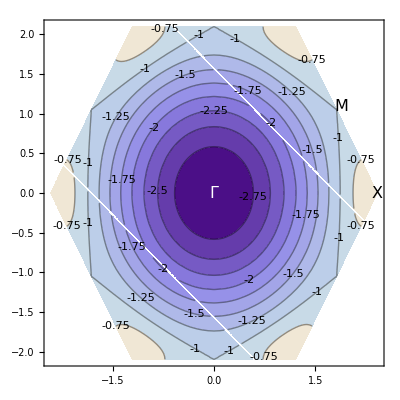

```mathematica
ContourPlot[EE[x+0.0,y+0.0,1,0.1][[1]],{x,-4Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{y,-2Pi/3,2Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤4Pi/3/Sqrt[3]],Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{(Pi+0.12)/Sqrt[3],(Pi+0.12)/3}],Black,Text[Style[X,16],{4Pi/3/Sqrt[3],0}]},ContourLabels->All]
```

```mathematica
Export["2D-1",%20,"JPEG"]
```

2D-1

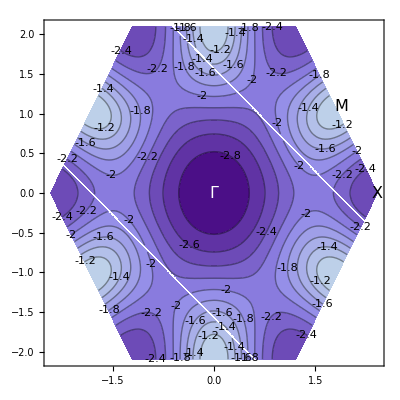

```mathematica
ContourPlot[EE[x+0.0,y+0.0,1,0.5][[1]],{x,-4Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{y,-2Pi/3,2Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤4Pi/3/Sqrt[3]],Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{(Pi+0.12)/Sqrt[3],(Pi+0.12)/3}],Black,Text[Style[X,16],{4Pi/3/Sqrt[3],0}]},ContourLabels->All]
```

```mathematica
Export["2D-2",%67,"JPEG"]
```

2D-2

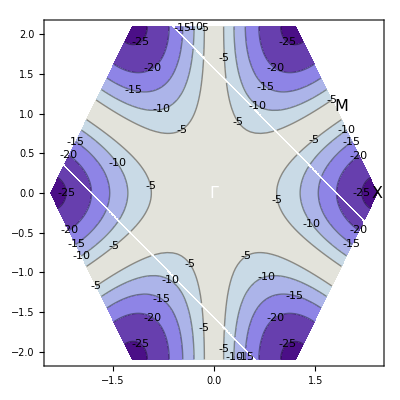

```mathematica
ContourPlot[EE[x+0.0,y+0.0,1,5][[1]],{x,-4Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{y,-2Pi/3,2Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤4Pi/3/Sqrt[3]],Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{(Pi+0.12)/Sqrt[3],(Pi+0.12)/3}],Black,Text[Style[X,16],{4Pi/3/Sqrt[3],0}]},ContourLabels->All]
```

```mathematica
Export["2D-3",%68,"JPEG"]
```

2D-3

### 1D plot (t=λ)

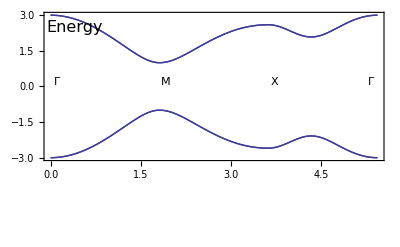

```mathematica
Plot[Piecewise[{{EE[t,t/Sqrt[3],1,0.5],t≥0&&t<Pi/Sqrt[3]},{EE[(t-Pi/Sqrt[3])/3+Pi/Sqrt[3],(2Pi/3-t/Sqrt[3]),1,0.5],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{EE[4/3(Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,1,0.5],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

```mathematica
Export["1D-1",%26,"JPEG"]
```

1D-1

### 1D plot (t=λ)

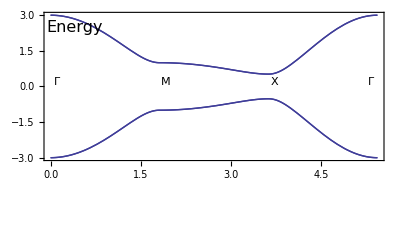

```mathematica
Plot[Piecewise[{{EE[t,t/Sqrt[3],1,0.1],t≥0&&t<Pi/Sqrt[3]},{EE[(t-Pi/Sqrt[3])/3+Pi/Sqrt[3],(2Pi/3-t/Sqrt[3]),1,0.1],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{EE[4/3(Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,1,0.1],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

```mathematica
Export["1D-2",%46,"JPEG"]
```

1D-2

### 1D plot (t=λ)

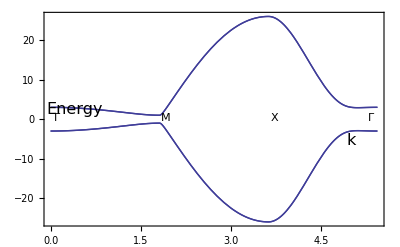

```mathematica
Plot[Piecewise[{{EE[t,t/Sqrt[3],1,5],t≥0&&t<Pi/Sqrt[3]},{EE[(t-Pi/Sqrt[3])/3+Pi/Sqrt[3],(2Pi/3-t/Sqrt[3]),1,5],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{EE[4/3(Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,1,5],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

```mathematica
Export["1D-3",%48,"JPEG"]
```

1D-3

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
F[x_,y_]:={EE[x,y,1,0.1][[1]],EE[x,y,1,0.1][[2]]}
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=F[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-3.2,-0.4},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-3.2,-0.4},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

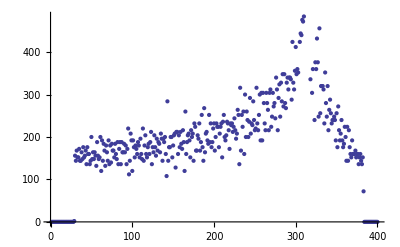

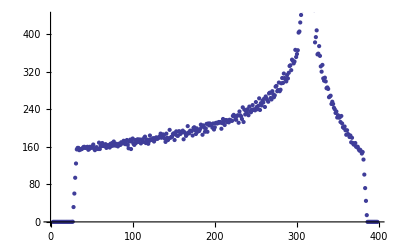

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```

```mathematica
Export["DOS-1",%54,"JPEG"]
```

DOS-1

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
F[x_,y_]:={EE[x,y,1,0.5][[1]],EE[x,y,1,0.5][[2]]}
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=F[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-3.2,-0.8},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-3.2,-0.8},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

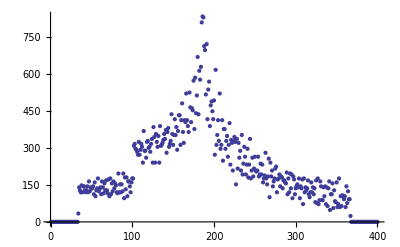

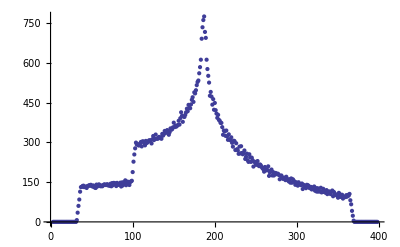

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```

```mathematica
Export["DOS-2.jpg",%87,"JPEG"]
```

DOS-2.jpg

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
F[x_,y_]:={EE[x,y,1,5][[1]],EE[x,y,1,5][[2]]}
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=F[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-25,0},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-25,0},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

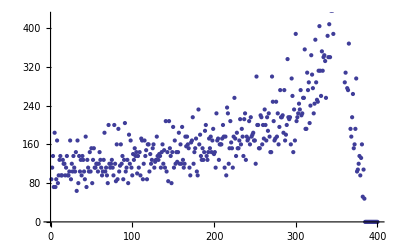

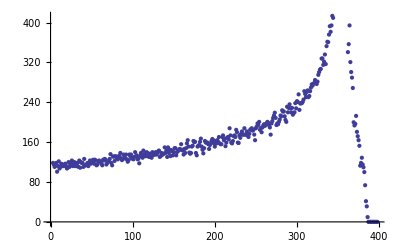

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```

```mathematica
Export["DOS-3.jpg",%66,"JPEG"]
```

DOS-3.jpg